```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<"ImportDMFE.wl"
Needs["DYNAMITE`"];
Needs["MaTeX`"];

texStyle={FontFamily->"Latin Modern Roman",FontSize->14};

style:={PlotStyle->Join[Lighter[Red,#]&/@Most[Subdivide[0.7,0.,10]],Darker[Red,#]&/@Most[Subdivide[0,0.7,10]]],Axes->False,AxesStyle->Directive[Black,FontSize->15,FontFamily->"Times"],Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameTicksStyle->{{Directive[FontFamily->"Times New Roman",FontSize->20,Black],Directive[FontOpacity->0,FontSize->0]},{Directive[FontFamily->"Times New Roman",FontSize->20,Black],Directive[FontOpacity->0,FontSize->0]}},ImageSize->Large,FrameStyle->Directive[Black,Thickness[.003]]};

styleInset:={PlotStyle->Join[Lighter[Red,#]&/@Most[Subdivide[0.7,0.,10]],Darker[Red,#]&/@Most[Subdivide[0,0.7,10]]],Axes->False,AxesStyle->Directive[Black,FontSize->12,FontFamily->"Times"],Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameTicksStyle->{{Directive[FontFamily->"Times New Roman",FontSize->15,Black],Directive[FontOpacity->0,FontSize->0]},{Directive[FontFamily->"Times New Roman",FontSize->15,Black],Directive[FontOpacity->0,FontSize->0]}},ImageSize->Large,FrameStyle->Directive[Black,Thickness[.003]]};

bsearch=Compile[{{list,_Complex,1},{elem,_Real}},Block[{n0=1,n1=Length[list],m=0,diff1},While[n0<=n1,m=Quotient[n0+n1,2];
If[list[[m]]==elem,Return[m]];
If[list[[m]]<elem,n0=m+1,n1=m-1]];
diff1=Abs[list[[m]]-elem];
If[list[[m]]<elem,If[diff1<=Abs[list[[Min[m+1,Length[list]]]]-elem],m,m+1],If[diff1<=Abs[list[[Max[m-1,1]]]-elem],m,m-1]]],RuntimeAttributes->{Listable},CompilationTarget->"C"];

LoadCompressed[file_String]:=Module[{try,rows,cols,cnt,data,s,headerBytes,fileBytes},try[htype_]:=Module[{},s=OpenRead[file,BinaryFormat->True];
rows=BinaryRead[s,htype,ByteOrdering->-1];
cols=BinaryRead[s,htype,ByteOrdering->-1];
If[!IntegerQ[rows]||!IntegerQ[cols]||rows<=0||cols<=0,Close[s];Return[$Failed]];
headerBytes=2*If[htype==="UnsignedInteger64",8,4];
fileBytes=FileByteCount[file];
cnt=rows*cols;
If[fileBytes<headerBytes+8 cnt,Close[s];Return[$Failed]];
data=BinaryReadList[s,"Real64",cnt,ByteOrdering->-1];
Close[s];
If[Length[data]==cnt,Partition[data,cols],$Failed]];
With[{m64=try["UnsignedInteger64"]},If[m64=!=$Failed,m64,try["UnsignedInteger32"]]]];
```

```mathematica
(*data=ImportDMFE["/nobackups/jlang/Results_CPC/02_12_2025_2120_p=3_q=3_lambda=0.50_T0=inf_G=0.00_L=512/data.h5"];*)
data=ImportDMFE["/nobackups/jlang/Results_CPC/04_12_2025_0128_p=3_q=3_lambda=0.50_T0=inf_G=0.00_L=512/data.h5"];
```

```mathematica
rvec=data["Data","rvec"];
t1grid=data["Data","t1grid"];
energy=Rest[Import["/nobackups/jlang/Results_CPC/04_12_2025_0128_p=3_q=3_lambda=0.50_T0=inf_G=0.00_L=512/energy.txt","Table"]][[All,-1]];
Etab=Transpose[{t1grid,energy}];
```

```mathematica
pos=DeleteDuplicates[bsearch[t1grid,2^Range[-10,21,.05]]];
Efunc[t_]=Interpolation[Developer`ToPackedArray[Etab[[pos]]],Method->"Spline",InterpolationOrder->5][t];
```

```mathematica
fλ[x_]:=x^3;
Eth:=Sqrt[Derivative[2][fλ][1]](fλ[1]/Derivative[2][fλ][1]-Derivative[1][fλ][1]/Derivative[2][fλ][1]-fλ[1]/Derivative[1][fλ][1]);
Block[{ind=100},FindFit[Transpose[{t1grid[[pos[[ind;;-1]]]],Log[Abs[(-t1grid[[pos[[ind;;-1]]]] Efunc'[t1grid[[pos[[ind;;-1]]]]])/(Efunc[t1grid[[pos[[ind;;-1]]]]]-Eth)-2/3]]}],{Log[Abs[α x^(-1/3)+β x^(-2/3)+γ x^-1]],-0.02<α<-0.01,0.3>β>.2,-.1>γ>-.2},{{α,-0.016},{β,0.25},{γ,-0.19}},x]]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{α→-0.0159544,β→0.248921,γ→-0.188888}

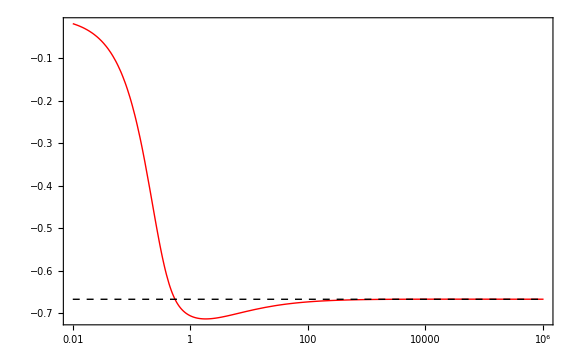

```mathematica
plot=Block[{α=-0.0159544,β=0.248921,γ=-0.188888},LogLinearPlot[{(x Efunc'[x])/(Efunc[x]-Eth),-2/3 },{x,.01,t1grid[[1350000]]},PlotStyle->{Directive[Red,Thick],Directive[Black,Dashed,Thick]},PlotRange->Full,Evaluate[style],FrameLabel->{MaTeX["t",Magnification->2.5],MaTeX["t\\partial_t\\log(E(t)-E_\\text{th})",Magnification->2.5]},Epilog->Inset[LogLogPlot[{Abs[α x^(-1/3)+β x^(-2/3)+γ x^-1],Abs[(-x Efunc'[x])/(Efunc[x]-Eth)-2/3] },{x,t1grid[[pos[[100]]]],t1grid[[1350000]]},PlotStyle->{Directive[Black,Thick],Directive[Red,Thick]},Evaluate[styleInset],FrameLabel->{MaTeX["t",Magnification->1.5],MaTeX["|t\\partial_t\\log(E(t)-E_\\text{th})+2/3|",Magnification->1.5]}],{Log[600],-.33},Center,14.5]]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","Energy.pdf"}],plot];
```

```mathematica
{t1grid512,times512, memory512}=Transpose[Rest[Import["/nobackups/jlang/Results_CPC/03_12_2025_0613_p=3_q=4_lambda=0.50_T0=inf_G=0.00_L=512/step_metrics.txt","Table"]]];
tfunc512[t_]=Interpolation[DeleteDuplicatesBy[Transpose[{t1grid512,times512-times512[[1]]}],First],InterpolationOrder->1][t];
memfunc512[t_]=Interpolation[DeleteDuplicatesBy[Transpose[{t1grid512,memory512}],First],InterpolationOrder->1][t];

{t1grid1024,times1024,memory1024}=Transpose[Rest[Import["/nobackups/jlang/Results_CPC/03_12_2025_0659_p=3_q=4_lambda=0.50_T0=inf_G=0.00_L=1024/step_metrics.txt","Table"]]];
tfunc1024[t_]=Interpolation[DeleteDuplicatesBy[Transpose[{t1grid1024,times1024-times1024[[1]]}],First],InterpolationOrder->1][t];
memfunc1024[t_]=Interpolation[DeleteDuplicatesBy[Transpose[{t1grid1024,memory1024}],First],InterpolationOrder->1][t];

{t1grid2048,times2048,memory2048}=Transpose[Rest[Import["/nobackups/jlang/Results_CPC/03_12_2025_1024_p=3_q=4_lambda=0.50_T0=inf_G=0.00_L=2048/step_metrics.txt","Table"]]];
tfunc2048[t_]=Interpolation[DeleteDuplicatesBy[Transpose[{t1grid2048,times2048-times2048[[1]]}],First],InterpolationOrder->1][t];
memfunc2048[t_]=Interpolation[DeleteDuplicatesBy[Transpose[{t1grid2048,memory2048}],First],InterpolationOrder->1][t];
```

```mathematica
{t1grid512,rvec512,C512}=Transpose[Rest[Import["/nobackups/jlang/Results_CPC/03_12_2025_0613_p=3_q=4_lambda=0.50_T0=inf_G=0.00_L=512/correlation.txt","Table"]]];

{t1grid1024,rvec1024,C1024}=Transpose[Rest[Import["/nobackups/jlang/Results_CPC/03_12_2025_0659_p=3_q=4_lambda=0.50_T0=inf_G=0.00_L=1024/correlation.txt","Table"]]];

{t1grid2048,rvec2048,C2048}=Transpose[Rest[Import["/nobackups/jlang/Results_CPC/03_12_2025_1024_p=3_q=4_lambda=0.50_T0=inf_G=0.00_L=2048/correlation.txt","Table"]]];
```

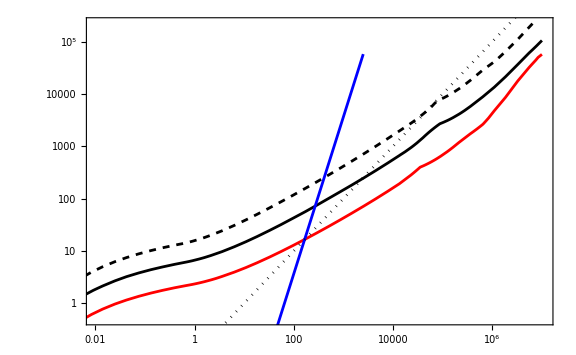

```mathematica
plot=Show[LogLogPlot[{tfunc512[t],tfunc1024[t],tfunc2048[t],0},{t,t1grid512[[2]],t1grid512[[-1]]},PlotRange->{{0.01,1.1Max[10^6,t1grid512[[-1]]]},{.5,1.1Max[200000,times512[[-1]]]}},PlotStyle->{Red,Black,Directive[{Black,Dashed}],Blue},Evaluate[style],FrameLabel->{MaTeX["\\text{simulated time}",Magnification->2.5],MaTeX["\\text{run time\\,[s]}",Magnification->2.5]},PlotLegends->Placed[{MaTeX["L=512",Magnification->1.6],MaTeX["L=1024",Magnification->1.6],MaTeX["L=2048",Magnification->1.6],MaTeX["\\text{Folena et al.}",Magnification->1.6]},{0.2,0.7}]],LogLogPlot[{36/9765625 x^3 HeavisideTheta[2500-x],1/10 x},{x,1/10,10^7},PlotStyle->{Blue,Directive[{Black,Dotted}]}]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","performanceGPU.pdf"}],plot];
```

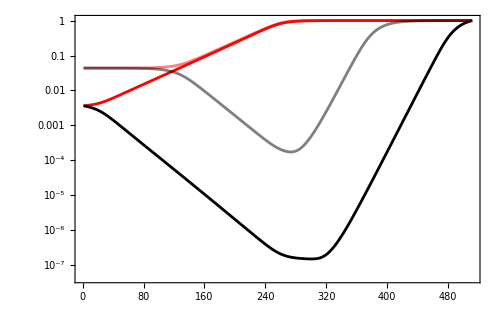

```mathematica
plot=ListLogPlot[{data["Data","QKv"][[bsearch[t1grid,10^6]]],data["Data","QRv"][[bsearch[t1grid,10^6]]],data["Data","QKv"][[bsearch[t1grid,10^3]]],data["Data","QRv"][[bsearch[t1grid,10^3]]]},Joined->True,PlotStyle->{Red,Black,Opacity[0.5,Red],Opacity[0.5,Black]},PlotLegends->Placed[{MaTeX["C(t_1,\\theta_i t_1)",Magnification->1.7],MaTeX["R(t_1,\\theta_i t_1)",Magnification->1.7]},{0.17,0.2}],FrameLabel->{MaTeX["i",Magnification->2.5]},ImageSize->500,Evaluate[style]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","CandR.pdf"}],plot];
```

```mathematica
pos=DeleteDuplicates[bsearch[t1grid,2^Range[-10,22,.05]]];
Rmin=Min[#]&/@data["Data","QRv"][[pos]];
Rfunc[t_]=Interpolation[Developer`ToPackedArray[Transpose[{t1grid[[pos]],Rmin}]],Method->"Spline",InterpolationOrder->5][t];
Rfunc2[t_]=Interpolation[Developer`ToPackedArray[Transpose[{t1grid[[pos]],LowpassFilter[(t1grid[[pos]] Rfunc'[t1grid[[pos]]])/(Rfunc[t1grid[[pos]]]-0),.1]}]],Method->"Spline",InterpolationOrder->5][t];
```

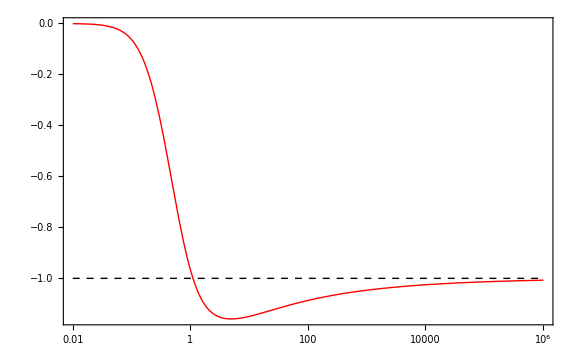

```mathematica
plot=LogLinearPlot[{Rfunc2[x] ,-1},{x,.01,t1grid[[1350000]]},PlotStyle->{Directive[Red,Thick],Directive[Black,Dashed,Thick]},PlotRange->Full,Evaluate[style],FrameLabel->{MaTeX["t",Magnification->2.5],MaTeX["t\\partial_t\\log(R_\\text{min}(t))",Magnification->2.5]},Epilog->Inset[LogLogPlot[{Abs[.3 x^-0.27],Abs[-Rfunc2[x]-1] },{x,t1grid[[pos[[100]]]],t1grid[[1350000]]},PlotStyle->{Directive[Black,Thick],Directive[Red,Thick]},Evaluate[styleInset],FrameLabel->{MaTeX["t",Magnification->1.5],MaTeX["|t\\partial_t\\log(R_\\text{min}(t))+1|"   ,Magnification->1.5]},Epilog->Inset[MaTeX["\\sim t^{-0.27}",Magnification->1.5],{Log[1000],Log[0.01]}]],{Log[850],-.5},Center,14]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","Rmin.pdf"}],plot];
```

```mathematica
Clear[Γ,c,g,μ];
Γ[t_]:=1/(2 t) Sum[k BesselI[k,4 t] T^(k-1),{k,0,50}];
dΓ[t_]=1/2 D[Log[Γ[t]],t];
c[t_?NumberQ,t1_?NumberQ]:=1/Sqrt[Γ[SetPrecision[t,40]] Γ[SetPrecision[t1,40]]] (BesselI[1,SetPrecision[2 (t+t1),40]]/(t+t1)+2 T NIntegrate[Γ[τ] BesselI[1,2 (t+t1-2 τ)]/(t+t1-2 τ),{τ,0,t1}]);
g[t_,t1_]:=Sqrt[Γ[SetPrecision[t1,40]]/Γ[SetPrecision[t,40]]] BesselI[1,SetPrecision[2 ((t-t1)+10^-40),40]]/((t-t1)+10^-40);
μ[t_]:=2NIntegrate[c[t,s] g[t,s],{s,0,t}]+T;
e[t_]:=-2NIntegrate[c[t,s] g[t,s],{s,0,t}];
eana[t_]=1/2(T-dΓ[t]);
```

```mathematica
(*data=ImportDMFE["/nobackups/jlang/Results_CPC/02_12_2025_2120_p=3_q=3_lambda=0.50_T0=inf_G=0.00_L=512/data.h5"];*)
dir="/nobackups/jlang/Results_CPC/03_12_2025_0043_p=2_q=2_lambda=0.50_T0=inf_G=0.50_L=512";
data512=ImportDMFE[FileNameJoin[{dir,"data.h5"}]];
κ=Sqrt[2];
T=1/(2κ);
t1grid512=Rest[Import[FileNameJoin[{dir,"rvec.txt"}],"Table"]][[All,1]];
θpoints512=Developer`ToPackedArray[1.Flatten[Import[FileNameJoin[{dir,"t1_compressed.txt"}],"Table"]]];
θpoints512*=1/θpoints512[[-1]];
θpoints512[[1]]=10.^-20;
energy512=Rest[Import[FileNameJoin[{dir,"energy.txt"}],"Table"]];
Efunc512[t_]=Interpolation[energy512,InterpolationOrder->3,Method->"Spline"][t];
dir="/nobackups/jlang/Results_CPC/03_12_2025_0509_p=2_q=2_lambda=0.50_T0=inf_G=0.50_L=512/"(*-e 1e-12*)
data512e=ImportDMFE[FileNameJoin[{dir,"data.h5"}]];
t1grid512e=Rest[Import[FileNameJoin[{dir,"rvec.txt"}],"Table"]][[All,1]];
θpoints512e=Developer`ToPackedArray[1.Flatten[Import[FileNameJoin[{dir,"t1_compressed.txt"}],"Table"]]];
θpoints512e*=1/θpoints512e[[-1]];
θpoints512e[[1]]=10.^-20;
energy512e=Rest[Import[FileNameJoin[{dir,"energy.txt"}],"Table"]];
Efunc512e[t_]=Interpolation[energy512e,InterpolationOrder->3,Method->"Spline"][t];
dir="/nobackups/jlang/Results_CPC/03_12_2025_0509_p=2_q=2_lambda=0.50_T0=inf_G=0.50_L=1024/"
data1024=ImportDMFE[FileNameJoin[{dir,"data.h5"}]];
t1grid1024=Rest[Import[FileNameJoin[{dir,"rvec.txt"}],"Table"]][[All,1]];
θpoints1024=Developer`ToPackedArray[1.Flatten[Import[FileNameJoin[{dir,"t1_compressed.txt"}],"Table"]]];
θpoints1024*=1/θpoints1024[[-1]];
θpoints1024[[1]]=10.^-20;
energy1024=Rest[Import[FileNameJoin[{dir,"energy.txt"}],"Table"]];
Efunc1024[t_]=Interpolation[energy1024,InterpolationOrder->3,Method->"Spline"][t];
```

/nobackups/jlang/Results_CPC/03_12_2025_0509_p=2_q=2_lambda=0.50_T0=inf_G=0.50_L=512/

/nobackups/jlang/Results_CPC/03_12_2025_0509_p=2_q=2_lambda=0.50_T0=inf_G=0.50_L=1024/

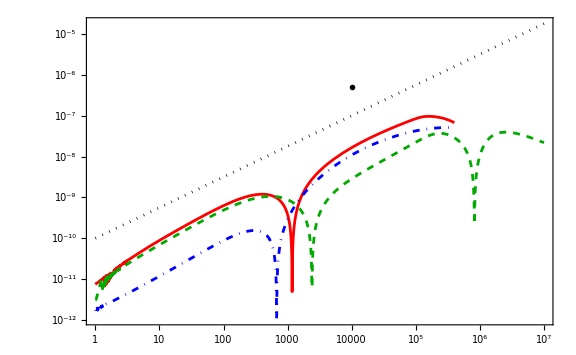

```mathematica
plot=LogLogPlot[{Abs[2/κ eana[κ t]-Efunc512[t]]HeavisideTheta[4*10^5-t],Abs[2/κ eana[κ t]-Efunc512e[t]]HeavisideTheta[4*10^5-t],Abs[2/κ eana[κ t]-Efunc1024[t]],10^-10 t^0.75},{t,1,10^7},PlotStyle->{Red,Directive[Blue,DotDashed],Directive[Darker[Green],Dashed],Directive[Black,Dotted]},FrameLabel->{MaTeX["t",Magnification->2.5],MaTeX["|E_\\text{num}(t)-E_\\text{ana}(t)|",Magnification->2.5]},Epilog->Inset[MaTeX["\\sim t",Magnification->1.8],{Log[10000],Log[5*10^-7]}],PlotLegends->Placed[{MaTeX["L=512",Magnification->1.6],MaTeX["L=512 \\text{ red. err.}",Magnification->1.6],MaTeX["L=1024",Magnification->1.6]},{0.23,0.8}],Evaluate[style]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","errorE.pdf"}],plot];
```

```mathematica
error512=Table[{t,Block[{tex=t1grid512[[bsearch[t1grid512,t]]]},g[κ tex,10^-40]-data512[["Data","QRv"]][[bsearch[t1grid512,t],1]]]},{t,2^Range[-5,18,0.05]}];
errorMid512=Table[{t,Block[{tex=t1grid512[[bsearch[t1grid512,t]]]},c[κ tex,κ tex θpoints512[[256]]]-data512[["Data","QKv"]][[bsearch[t1grid512,t],256]]]},{t,2^Range[-5,18,0.05]}];

error512e=Table[{t,Block[{tex=t1grid512e[[bsearch[t1grid512e,t]]]},g[κ tex,10^-40]-data512e[["Data","QRv"]][[bsearch[t1grid512e,t],1]]]},{t,2^Range[-5,18,0.05]}];
errorMid512e=Table[{t,Block[{tex=t1grid512e[[bsearch[t1grid512e,t]]]},c[κ tex,κ tex θpoints512e[[256]]]-data512e[["Data","QKv"]][[bsearch[t1grid512e,t],256]]]},{t,2^Range[-5,18,0.05]}];

error1024=Table[{t,Block[{tex=t1grid1024[[bsearch[t1grid1024,t]]]},g[κ tex,10^-40]-data1024[["Data","QRv"]][[bsearch[t1grid1024,t],1]]]},{t,2^Range[-5,24,0.05]}];
errorMid1024=Table[{t,Block[{tex=t1grid1024[[bsearch[t1grid1024,t]]]},c[κ tex,κ tex θpoints1024[[512]]]-data1024[["Data","QKv"]][[bsearch[t1grid1024,t],512]]]},{t,2^Range[-5,24,0.05]}];
```

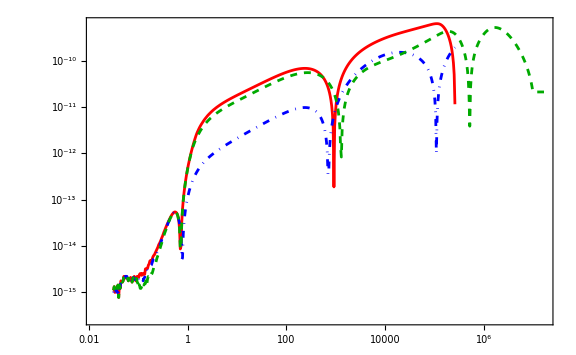

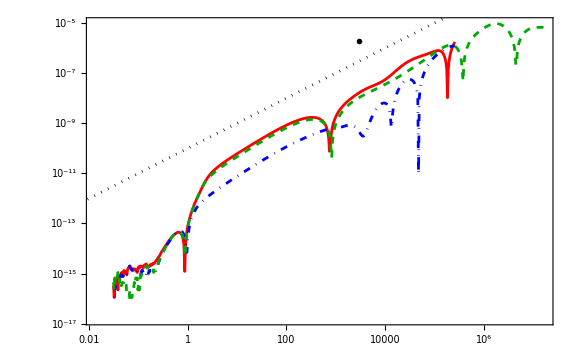

```mathematica
plot=ListLogLogPlot[{Abs[error512],Abs[error512e],Abs[error1024]},Joined->True,PlotStyle->{Red,Directive[Blue,DotDashed],Directive[Darker[Green],Dashed],Directive[Black,Dotted]},FrameLabel->{MaTeX["t",Magnification->2.5],MaTeX["|R_\\text{num}(t,0)-R_\\text{ana}(t,0)|",Magnification->2.5]},Epilog->Inset[MaTeX["\\sim t",Magnification->1.8],{Log[10000],Log[5*10^-7]}],PlotLegends->Placed[{MaTeX["L=512",Magnification->1.6],MaTeX["L=512 \\text{ red. err.}",Magnification->1.6],MaTeX["L=1024",Magnification->1.6]},{0.77,0.2}],Evaluate[style]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","errorR.pdf"}],plot];
plot=Show[ListLogLogPlot[{Abs[errorMid512],Abs[errorMid512e],Abs[errorMid1024]},Joined->True,PlotStyle->{Red,Directive[Blue,DotDashed],Directive[Darker[Green],Dashed],Directive[Black,Dotted]},FrameLabel->{MaTeX["t",Magnification->2.5],MaTeX["|C_\\text{num}(t,t/2)-C_\\text{ana}(t,t/2)|",Magnification->2.5]},Epilog->Inset[MaTeX["\\sim t",Magnification->1.8],{Log[3000],Log[2*10^-6]}],PlotLegends->Placed[{MaTeX["L=512",Magnification->1.6],MaTeX["L=512 \\text{ red. err.}",Magnification->1.6],MaTeX["L=1024",Magnification->1.6]},{0.23,0.8}],Evaluate[style]],LogLogPlot[10^-10 t,{t,10^-10,10^10},PlotStyle->Directive[Black,Dotted]]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","errorC.pdf"}],plot];
```

```mathematica
(*LogLogPlot[{Efunc512[t]-(1/2. T-1)2/κ,3/8 t^-1},{t,1,4*10^5}]
Block[{t=10^5},Block[{tex=t1grid512[[bsearch[t1grid512,t]]]},ListPlot[{c[κ tex,κ tex#]&/@θpoints512-data512[["Data","QKv"]][[bsearch[t1grid512,t]]]},Joined->True,PlotRange->Full]]]
Block[{t=10^5},Block[{tex=t1grid512[[bsearch[t1grid512,t]]]},ListLogPlot[Abs[g[κ tex,κ tex#]&/@θpoints512-data512[["Data","QRv"]][[bsearch[t1grid512,t]]]],Joined->True,PlotRange->Full]]]*)
```

```mathematica
Clear[Intθ3,Intθ5,sectionInt,diff,splineCoeffs];
Intθ3:=Prepend[Accumulate[# . secInt3],0]&;
Intθ5:=Prepend[Accumulate[# . secInt5],0]&;
diff:=Rest[#]-Most[#]&;

sectionInt[{points_,prec_:MachinePrecision}]:=Module[{interp3,interp5,I1,I2,dω,pts},
pts=SetPrecision[points,prec];
dω=diff[pts];
(*Cubic interpolation *)
interp3=splineCoeffs[{pts,0,prec,0}];
(*quintic interpolation *)
interp5=splineCoeffs[{pts,0,prec,0},"Five"->True];
(*integrate over each interval with two different "weight" functions*)
(*Integrate[x^m,{x,0,a}]*)
I1=1/(#+1) Power[dω,#+1]&/@Range[0,5];
(*FullSimplify[Table[Integrate[x^mSin[2π x/a],{x,0,a},Assumptions->{m≥0,m∈Integers,a>0}],{m,0,5}]]*)
(*Build and output inteval integration matrices*)
Chop[{Transpose[Total[I1[[;;4]] interp3]],Transpose[Total[I1 interp5]]},10^-20]];

SyntaxInformation[splineCoeffs]={"ArgumentsPattern"->{_,OptionsPattern[]}};
SetAttributes[splineCoeffs,HoldAll];
Options[splineCoeffs]={"Five"->False,"Last"->False,"All"->False,"Mixed"->True};
splineCoeffs::padInput="interpolation matrices cannot be generated from a precomputed second-highest coefficient matrix when the padding is set to be non-zero.";
splineCoeffs[{points_,cmatIn_:0,precIn_:precision,padding_:15},opts:OptionsPattern[]]:=
Module[{pts,h,rot,n,id,amat,bmat,cmat,cmat2,dmat,emat,emat2,fmat,prec,padfc,padfcT,mixed},
mixed=OptionValue["Mixed"]&&(!OptionValue["Last"])&&(padding!=0);
(* check that the input is well defined *)
If[!(cmatIn===0)&&padding!=0,Message[splineCoeffs::padInput];,
(*Padding*)
padfc[x_]:=x[[All,If[points[[1]]>=0,1,padding+1];;-padding-1]];
padfcT[x_]:=If[Length[x]>Length[points],x[[If[points[[1]]>=0,1,padding+1];;-padding-1]],x];
(*Use the precision of input if a cmatIn is given*)
prec=If[cmatIn===0,precIn,Precision[cmatIn]];
(*pad input grid symmetrically if the grid has negative values otherwise only pad the end of the grid*)
pts=SetPrecision[Join[If[points[[1]]>=0,points,Join[points[[1]]-Reverse[Range[padding]],points]],points[[-1]]+Range[padding]],prec];
h=Subtract[RotateLeft[pts],pts];
n=Length[pts];

(* rot is the difference operator: Δ *)
rot=SparseArray[{Band[{1,1}]->-1,Band[{1,2}]->1},{n,n}];
	id=SparseArray[{Band[{1,1}]->1},{n,n}];
If[!OptionValue["Five"],
(*Cubic Spline*)
Module[{g0c,g1c,coefc,coefc2,Bc,Bc2,Δω},
g0c=1/3 rot;
g1c=(id+g0c)(3h);
(*N-3 equations from continuity *)
coefc=(Most[(6h)id]+Most[(9h)g0c]+diff[g1c])/Most[h];
Bc=diff[rot/((1/3)h)]/Most[h];
If[mixed,coefc2=coefc[[If[points[[1]]>=0,1,padding+1];;-padding-1,If[points[[1]]>=0,1,padding+1];;-padding-1]];coefc2=SetPrecision[SparseArray[Catenate[Normal/@{{2id[[If[points[[1]]>=0,1,padding+1],If[points[[1]]>=0,1,padding+1];;-padding-1]]+RotateRight[id[[If[points[[1]]>=0,1,padding+1],If[points[[1]]>=0,1,padding+1];;-padding-1]]]},Most[coefc2],{2id[[-padding-1,If[points[[1]]>=0,1,padding+1];;-padding-1]]+RotateLeft[id[[-padding-1,If[points[[1]]>=0,1,padding+1];;-padding-1]]]}}]],prec];];
coefc=SetPrecision[SparseArray[Catenate[Normal/@{{2id[[1]]+RotateRight[id[[1]]]},Most[coefc],{2id[[-1]]+RotateLeft[id[[-1]]]}}]],prec];
Bc=SetPrecision[SparseArray[With[{zer=ConstantArray[0,If[points[[1]]>=0,n-padding,n-2padding]]},Catenate[{{zer},Most[padfc[Normal[Bc]]],{zer}}]]],prec];
Bc2=Bc[[If[points[[1]]>=0,1,padding+1];;-padding-1]];
Bc2[[{-1,1}]]*=0;
If[cmatIn===0,cmat=LinearSolve[coefc,Bc];If[mixed,cmat2=LinearSolve[coefc2,Bc2]],cmat=cmatIn;
If[!SquareMatrixQ[cmat],cmat=ArrayFlatten[{{cmat},{{-cmat[[-1]]/2}}}]];];
dmat=diff[cmat]/(3 Most[h]);
If[!OptionValue["Last"],
rot=padfc[rot];
id=padfc[id];
Δω=Most[h];
bmat=Most[rot]/Δω-Δω(Most[cmat]+diff[cmat]/3);
amat=Most[id];
cmat=If[mixed,cmat2,Most[cmat]]]];
,
(*Quintic spline*) 
Module[{g0q,g1q,g2q,g3q,coefq,coefq2,Bq,Bq2,Δω},g0q=1/5 rot;
g1q=g0q+id;
g2q= (id(2 h^2))[[;;-2]](3h[[2;;]]+2h[[;;-2]])+((5h^2)g0q)[[;;-2]](2h[[2;;]]+h[[;;-2]])+diff[g1q h^3];g3q=(id (2h))[[;;-3]](3h[[;;-3]]+4h[[2;;-2]]+2h[[3;;]])+g0q[[;;-3]]((10h[[;;-3]])(h[[;;-3]]+2h[[2;;-2]]+h[[3;;]]))+diff[1/(h[[;;-2]]+h[[2;;]])(((id (4h))[[;;-2]]+ g0q[[;;-2]] (10h[[;;-2]]))h[[2;;]]^2+g2q)];

(* Find matrix equation for second highest coefficient matrix if it is not given as input *)
If[cmatIn===0,
coefq=1/(h[[;;-4]]+h[[2;;-3]]+h[[3;;-2]]+h[[4;;]])((id (4h))[[;;-4]]+g0q[[;;-4]](10h[[;;-4]])+diff[1/(h[[;;-3]]+h[[2;;-2]]+h[[3;;]])g3q]);
Bq=1/(h[[;;-4]]+h[[2;;-3]]+h[[3;;-2]]+h[[4;;]])diff[1/(h[[;;-3]]+h[[2;;-2]]+h[[3;;]])diff[1/(h[[;;-2]]+h[[2;;]])diff[rot/h ]]];
If[mixed,coefq2=coefq[[If[points[[1]]>=0,1,padding+1];;-padding-1,If[points[[1]]>=0,1,padding+1];;-padding-1]];coefq2=SetPrecision[SparseArray[Catenate[Normal/@{id[[If[points[[1]]>=0,1,padding+1];;If[points[[1]]>=0,1,padding+1]+1,If[points[[1]]>=0,1,padding+1];;-padding-1]],Most[coefq2],id[[-padding-2;;-padding-1,If[points[[1]]>=0,1,padding+1];;-padding-1]]}]],prec];];
coefq=SetPrecision[SparseArray[Catenate[Normal/@{id[[;;2]],coefq[[;;-2]],id[[-2;;]]}]],prec];
Bq=SetPrecision[SparseArray[With[{zer=ConstantArray[0,{n,n}]},padfc[Catenate[{zer[[;;2]],Normal[Bq[[;;-2]]],zer[[-2;;]]}]]]],prec];
Bq2=Bq[[If[points[[1]]>=0,1,padding+1];;-padding-1]];
Bq2[[1;;2]]*=0;
Bq2[[-2;;-1]]*=0;
emat=Chop[LinearSolve[coefq,Bq],10^-200];
If[mixed,emat2=Chop[LinearSolve[coefq2,Bq2],10^-200]];
,If[!SquareMatrixQ[emat],emat=ArrayFlatten[{{cmatIn},{{SparseArray[{},{n}]}}}]];];
If[!OptionValue["Last"],
(* Matrices to generate coefficients *)
Δω=Most[h];
fmat=diff[emat]/(5Δω);
rot=padfc[rot];
id=padfc[id];
(* Compute the N-3 A3 coefficients using the inverted equations. 
The last two coefficients (N-2,N-1) are then computed from the continuity equations *)
dmat=Catenate[FoldList[{(#1[[-1]]+(4 Δω[[#2]]) emat[[#2-1]]+(10 Δω[[#2]]^2) fmat[[#2]])}&,#,{-3,-2}]&@((diff[diff[Most[rot]/Δω]/(Most[Δω]+Rest[Δω])]-Most[g3q . emat])/(Δω[[;;-3]]+Δω[[2;;-2]]+Δω[[3;;]]))];
(* Compute the N-2 A2 coefficients using the inverted equations. 
The last coefficient (j=N-1)is then computed from the continuity equations *)
cmat=Catenate[FoldList[{(#1[[-1]]+(3Δω[[#2]])dmat[[#2]]+(6Δω[[#2]]^2)emat[[#2-1]]+(10 Δω[[#2]]^3)fmat[[#2]])}&,#,{-2}]&@((diff[Most[rot]/Δω]-diff[Δω^2 dmat]-Most[g2q . emat])/(Most[Δω]+Rest[Δω])-(3 Most[Δω])Most[dmat])];
bmat=Most[rot]/Δω-Δω cmat-Δω^2 dmat-Δω^3 Most[g1q . emat];
amat=Most[id];
emat=If[mixed,emat2,Most[emat]];
,fmat=diff[emat]/(5 Most[h]);emat=Most[emat];]]];
If[!OptionValue["Last"],If[OptionValue["Five"],SparseArray[Threshold[If[OptionValue["All"],#,padfcT[#]],10^-Max[prec,30]]]&/@{amat,bmat,cmat,dmat,emat,fmat},SparseArray[Threshold[If[OptionValue["All"],#,padfcT[#]],10^-Max[prec,30]]]&/@{amat,bmat,cmat,dmat}],If[OptionValue["Five"],SparseArray[Threshold[If[OptionValue["All"],fmat,padfcT[fmat]],10^-Max[prec,30]]],SparseArray[Threshold[If[OptionValue["All"],dmat,padfcT[dmat]],10^-Max[prec,30]]]]]]];

χ[R_,t_]:=Block[{temp=t*Intθ5[R]},temp[[-1]]-temp];

fλ[x_]:=x^3;
γ=0.5;
q1:=Block[{q0},If[γ!=0,q0/.NSolve[{1/(1-q0)^2-Derivative[2][fλ][q0]/γ^2==0,1>q0>0},q0][[-1]],1]];
xth:=If[γ!=0,1/(1/γ Derivative[1][fλ][q1](1-q1))+1/γ (q1-1)/q1,(Sqrt[Derivative[2][fλ][1]]/Derivative[1][fλ][1]-1/Sqrt[Derivative[2][fλ][1]])];
```

```mathematica
dir="/nobackups/jlang/Results_CPC/02_12_2025_2122_p=3_q=3_lambda=0.50_T0=inf_G=0.50_L=512/";
data=ImportDMFE[FileNameJoin[{dir,"data.h5"}]];
t1grid=Rest[Import[FileNameJoin[{dir,"rvec.txt"}],"Table"]][[All,1]];
θpoints=Developer`ToPackedArray[1.Flatten[Import[FileNameJoin[{dir,"t1_compressed.txt"}],"Table"]]];
θpoints*=1/θpoints[[-1]];
{secInt3,secInt5}=sectionInt[{θpoints}];
```

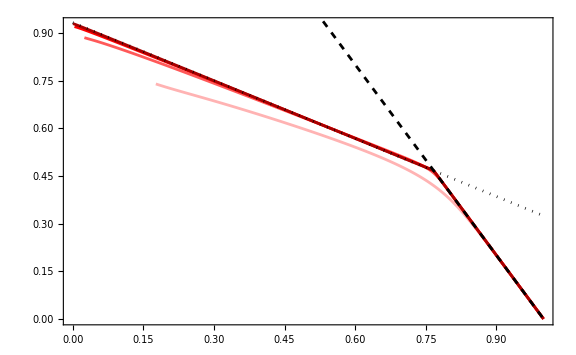

```mathematica
plot=Show[ListPlot[Table[Transpose[{data[["Data","QKv"]][[bsearch[t1grid,t]]],χ[data[["Data","QRv"]][[bsearch[t1grid,t]]],t]}],{t,10^Range[1,7,2]}],Joined->True,FrameLabel->{MaTeX["C",Magnification->2.5],MaTeX["\\chi",Magnification->2.5]},PlotLegends->Placed[MaTeX["t=10^{"<>ToString[#]<>"}",Magnification->1.6]&/@Range[1,7,2],{0.23,0.3}],PlotStyle->Join[Lighter[Red,#]&/@Most[Subdivide[0.7,0.,2]],Darker[Red,#]&/@Most[Subdivide[0,0.7,2]]],Evaluate[style]],Plot[{2-2x,0.9323562961364702-xth x},{x,0,1},PlotStyle->{Directive[Black,Dashed],Directive[Black,Dotted]}]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","RvsC.pdf"}],plot];
```

0.405003

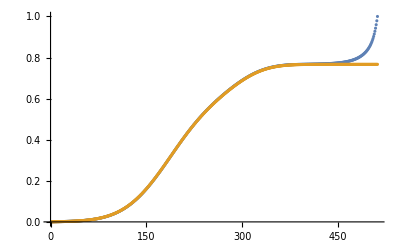

```mathematica
func[α_]=Norm[data[["Data","QKv"]][[-1,1;;bsearch[θpoints,1-t1grid[[-1]]^(-1/3)]]]-q1 θpoints[[1;;bsearch[θpoints,1-t1grid[[-1]]^(-1/3)]]]^α];
α=α/.FindMinimum[func[α],{α,0.35,0.45}][[2]]
ListPlot[{data[["Data","QKv"]][[-1]],q1 θpoints^α}]
```

```mathematica
C1[t_]=Block[{i=1},Interpolation[Transpose[{t1grid,data[["Data","QKv"]][[All,i]]-q1 θpoints[[i]]^α}],InterpolationOrder->3,Method->"Spline"]][t];
C100[t_]=Block[{i=137},Interpolation[Transpose[{t1grid,data[["Data","QKv"]][[All,i]]-q1 θpoints[[i]]^α}],InterpolationOrder->3,Method->"Spline"]][t];
C200[t_]=Block[{i=184},Interpolation[Transpose[{t1grid,data[["Data","QKv"]][[All,i]]-q1 θpoints[[i]]^α}],InterpolationOrder->3,Method->"Spline"]][t];
C300[t_]=Block[{i=257},Interpolation[Transpose[{t1grid,data[["Data","QKv"]][[All,i]]-q1 θpoints[[i]]^α}],InterpolationOrder->3,Method->"Spline"]][t];
C400[t_]=Block[{i=329},Interpolation[Transpose[{t1grid,data[["Data","QKv"]][[All,i]]-q1 θpoints[[i]]^α}],InterpolationOrder->3,Method->"Spline"]][t];
```

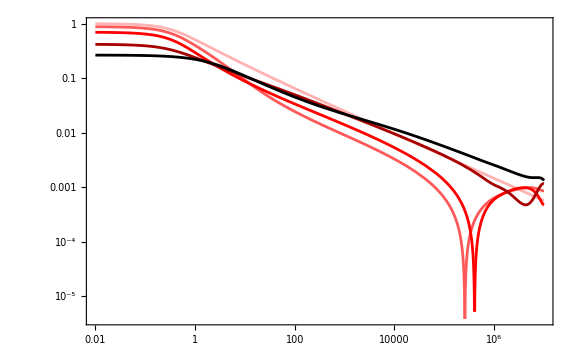

```mathematica
plot=LogLogPlot[{Abs[C1[t]],Abs[C100[t]],Abs[C200[t]],Abs[C300[t]],Abs[C400[t]]},{t,.01,10^7},FrameLabel->{MaTeX["t",Magnification->2.5],MaTeX["|C(t,\\theta t)-\\theta^\\alpha|",Magnification->2.5]},PlotLegends->Placed[MaTeX["\\theta="<>ToString[#],Magnification->1.6]&/@{0,0.01,0.1,0.5,0.9},{0.15,0.33}],PlotStyle->Join[Lighter[Red,#]&/@Most[Subdivide[0.7,0.,2]],Darker[Red,#]&/@Most[Subdivide[0,0.7,2]],{Black}],Evaluate[style]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","agingConvergence.pdf"}],plot];
```

```mathematica
dir="/nobackups/jlang/Results_CPC/03_12_2025_2147_p=3_q=3_lambda=0.50_T0=inf_G=0.00_L=512/";
data=ImportDMFE[FileNameJoin[{dir,"data.h5"}]];
t1grid=Rest[Import[FileNameJoin[{dir,"rvec.txt"}],"Table"]][[All,1]];
θpoints=Developer`ToPackedArray[1.Flatten[Import[FileNameJoin[{dir,"t1_compressed.txt"}],"Table"]]];
θpoints*=1/θpoints[[-1]];
{secInt3,secInt5}=sectionInt[{θpoints}];
```

0.353747

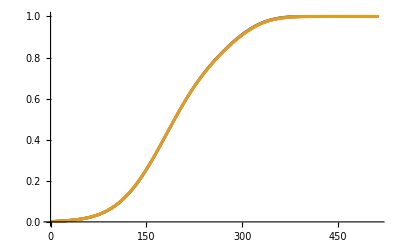

```mathematica
γ=0;
Clear[α]
func[α_]=Norm[data[["Data","QKv"]][[-1,bsearch[θpoints,t1grid[[-1]]^(-1/3)];;bsearch[θpoints,1-t1grid[[-1]]^(-1/3)]]]-q1 θpoints[[bsearch[θpoints,t1grid[[-1]]^(-1/3)];;bsearch[θpoints,1-t1grid[[-1]]^(-1/3)]]]^α];
α=α/.FindMinimum[func[α],{α,0.33,0.45}][[2]]
ListPlot[{data[["Data","QKv"]][[-1]],q1 θpoints^α}]
```

```mathematica
C1[t_]=Block[{i=1},Interpolation[Transpose[{t1grid,data[["Data","QKv"]][[All,i]]-q1 θpoints[[i]]^α}],InterpolationOrder->3,Method->"Spline"]][t];
C100[t_]=Block[{i=137},Interpolation[Transpose[{t1grid,data[["Data","QKv"]][[All,i]]-q1 θpoints[[i]]^α}],InterpolationOrder->3,Method->"Spline"]][t];
C200[t_]=Block[{i=184},Interpolation[Transpose[{t1grid,data[["Data","QKv"]][[All,i]]-q1 θpoints[[i]]^α}],InterpolationOrder->3,Method->"Spline"]][t];
C300[t_]=Block[{i=257},Interpolation[Transpose[{t1grid,data[["Data","QKv"]][[All,i]]-q1 θpoints[[i]]^α}],InterpolationOrder->3,Method->"Spline"]][t];
C400[t_]=Block[{i=329},Interpolation[Transpose[{t1grid,data[["Data","QKv"]][[All,i]]-q1 θpoints[[i]]^α}],InterpolationOrder->3,Method->"Spline"]][t];
```

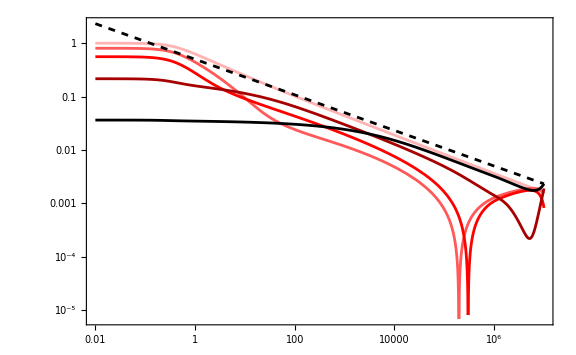

```mathematica
plot=LogLogPlot[{Abs[C1[t]],Abs[C100[t]],Abs[C200[t]],Abs[C300[t]],Abs[C400[t]],1/2 t^(-1/3)},{t,.01,10^7},FrameLabel->{MaTeX["t",Magnification->2.5],MaTeX["|C(t,\\theta t)-\\theta^\\alpha|",Magnification->2.5]},PlotLegends->Placed[MaTeX["\\theta="<>ToString[#],Magnification->1.6]&/@{0,0.01,0.1,0.5,0.9},{0.15,0.33}],PlotStyle->Join[Lighter[Red,#]&/@Most[Subdivide[0.7,0.,2]],Darker[Red,#]&/@Most[Subdivide[0,0.7,2]],{Black,Directive[Black,Dashed]}],Evaluate[style]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","agingConvergenceZeroTemp.pdf"}],plot];
```

```mathematica
dir="/nobackups/jlang/Results_CPC/03_12_2025_0613_p=3_q=4_lambda=0.50_T0=inf_G=0.00_L=512/"
data=ImportDMFE[FileNameJoin[{dir,"data.h5"}]];
t1grid=Rest[Import[FileNameJoin[{dir,"rvec.txt"}],"Table"]][[All,1]];
θpoints=Developer`ToPackedArray[1.Flatten[Import[FileNameJoin[{dir,"t1_compressed.txt"}],"Table"]]];
θpoints*=1/θpoints[[-1]];
θpoints34=θpoints;
{secInt3,secInt5}=sectionInt[{θpoints}];
```

/nobackups/jlang/Results_CPC/03_12_2025_0613_p=3_q=4_lambda=0.50_T0=inf_G=0.00_L=512/

```mathematica
Clear[createInt];
Options[createInt]={"Five"->False};
createInt[{τpts_,cmatIn_:0,prec_:precision},opts:OptionsPattern[]]:=Quiet[Block[{IL4jk,IL6jk,f0,f1,f2,f3,f4,f5,Len=Length[τpts]},
f0[ω1_,ω2_]:=-ω1+ω2;
f1[ω1_,ω2_]:=(1/2) (ω2-ω1)^2;
f2[ω1_,ω2_]:=(1/3) (ω2-ω1)^3;
f3[ω1_,ω2_]:=(1/4) (ω2-ω1)^4;
f4[ω1_,ω2_]:=(1/5) (ω2-ω1)^5;
f5[ω1_,ω2_]:=(1/6) (ω2-ω1)^6;
If[OptionValue["Five"],IL6jk=SetPrecision[{f0[Most[τpts],Rest[τpts]],f1[Most[τpts],Rest[τpts]],f2[Most[τpts],Rest[τpts]],f3[Most[τpts],Rest[τpts]],f4[Most[τpts],Rest[τpts]],f5[Most[τpts],Rest[τpts]]},prec],IL4jk=SetPrecision[{f0[Most[τpts],Rest[τpts]],f1[Most[τpts],Rest[τpts]],f2[Most[τpts],Rest[τpts]],f3[Most[τpts],Rest[τpts]]},prec]];
Integrator= Accumulate[Prepend[Total[MapThread[Times,{If[OptionValue["Five"],IL6jk,IL4jk],splineCoeffs[{τpts,cmatIn,prec,0},"Five"->OptionValue["Five"]]+10.^-200}]],SparseArray[{},Length[τpts]]]];
int=Developer`ToPackedArray[Integrator[[-1]]]]];

T0=∞;
fλ[x_]:=1/2(x^3+x^4);
Observable[n_,QK_,QR_,t_]:=t (Derivative[n][fλ][QK]*QR) . int+1/T0 Derivative[n-1][fλ][If[MatrixQ[QK],QK[[All,1]],QK[[1]]]];
En[n_,QK_,QR_,t_]:=n/2 t (QK^(n-1)*QR) . int;

precision=MachinePrecision;
createInt[{θpoints},"Five"->True];

Eth:=Sqrt[Derivative[2][fλ][1]](fλ[1]/Derivative[2][fλ][1]-Derivative[1][fλ][1]/Derivative[2][fλ][1]-fλ[1]/Derivative[1][fλ][1]);
```

```mathematica
E3=En[3,data[["Data","QKv"]],data[["Data","QRv"]],t1grid];
E4=En[4,data[["Data","QKv"]],data[["Data","QRv"]],t1grid];
E34func[t_]=Interpolation[Transpose[{E3,E4}],Method->"Spline",InterpolationOrder->3][t];
```

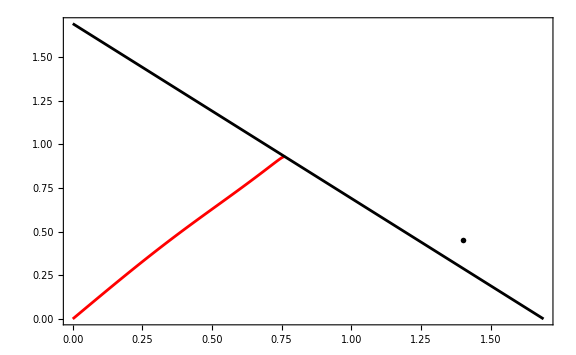

```mathematica
plot=Show[Plot[E34func[t],{t,0,E34func["Domain"][[1,2]]},PlotRange->{{0,-Eth},{0,-Eth}},PlotStyle->Red,Evaluate[style],FrameLabel->{MaTeX["E_4",Magnification->2.5],MaTeX["E_3",Magnification->2.5]},Epilog->Inset[MaTeX["E_\\text{th}",Magnification->2],{1.4,0.45}]],Plot[-Eth-x,{x,0,-Eth},PlotStyle->Black]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","E34.pdf"}],plot];
```

```mathematica
dir="/nobackups/jlang/Results_CPC/03_12_2025_1938_p=3_q=9_lambda=0.50_T0=inf_G=0.00_L=2048/"
data39=ImportDMFE[FileNameJoin[{dir,"data.h5"}]];
t1grid39=Rest[Import[FileNameJoin[{dir,"rvec.txt"}],"Table"]][[All,1]];
θpoints2048=Developer`ToPackedArray[1.Flatten[Import[FileNameJoin[{dir,"t1_compressed.txt"}],"Table"]]];
θpoints2048*=1/θpoints2048[[-1]];
{secInt3,secInt5}=sectionInt[{θpoints2048}];
energy=Rest[Import[FileNameJoin[{dir,"energy.txt"}],"Table"]];
Efunc[t_]=Interpolation[energy,InterpolationOrder->3,Method->"Spline"][t];
```

/nobackups/jlang/Results_CPC/03_12_2025_1938_p=3_q=9_lambda=0.50_T0=inf_G=0.00_L=2048/

```mathematica
fλ[x_]:=1/2(x^3+x^9);
γ=0;
createInt[{θpoints2048},"Five"->True];
E3=En[3,data39[["Data","QKv"]],data39[["Data","QRv"]],t1grid39];
E9=En[9,data39[["Data","QKv"]],data39[["Data","QRv"]],t1grid39];
E39func[t_]=Interpolation[DeleteDuplicatesBy[Transpose[{E3,E9}][[1;;800000;;2]],First],Method->"Spline",InterpolationOrder->3][t];
```

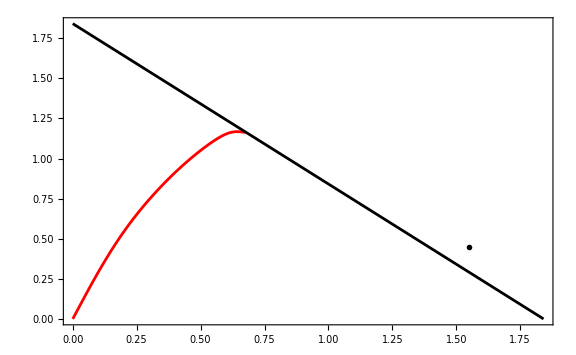

```mathematica
plot=Show[Plot[E39func[t],{t,0,E39func["Domain"][[1,2]]},PlotRange->{{0,-Eth},{0,-Eth}},PlotStyle->Red,Evaluate[style],FrameLabel->{MaTeX["E_9",Magnification->2.5],MaTeX["E_3",Magnification->2.5]},Epilog->Inset[MaTeX["E_\\text{th}",Magnification->2],{1.55,0.45}]],Plot[-Eth-x,{x,0,-Eth},PlotStyle->Black]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","E39.pdf"}],plot];
```

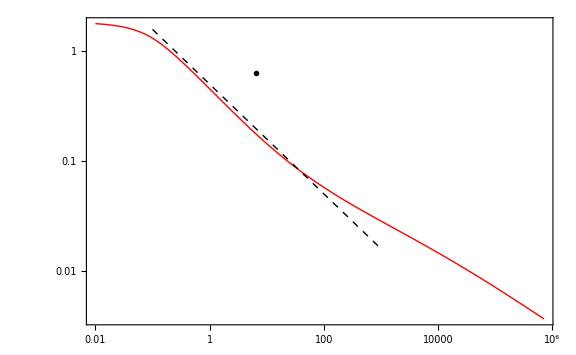

```mathematica
plot=LogLogPlot[{Abs[Efunc[x]-Eth],1/2 x^(-1/2)HeavisideTheta[x-0.1]HeavisideTheta[1000-x]},{x,.01,t1grid[[-1]]},PlotStyle->{Directive[Red,Thick],Directive[Black,Dashed,Thick]},PlotRange->Full,Evaluate[style],FrameLabel->{MaTeX["t",Magnification->2.5],MaTeX["E(t)-E_\\text{th}",Magnification->2.5]},Epilog->Inset[MaTeX["\\sim t^{-1/2}",Magnification->2],{1.85,-0.45}]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","mixedEnergyConvergence.pdf"}],plot];
```

```mathematica
Cfunc[θ_]=Interpolation[Transpose[{θpoints2048,data39[["Data","QKv"]][[300000]]}],InterpolationOrder->3,Method->"Spline"][θ];
Rfunc[θ_]=Interpolation[Transpose[{θpoints2048,data39[["Data","QRv"]][[300000]]}],InterpolationOrder->1,Method->"Spline"][θ];
```

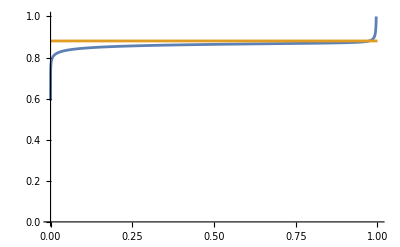

```mathematica
Plot[{(t1grid39[[300000]]Rfunc[θ])/Cfunc'[θ],xth},{θ,0,1},PlotRange->{0,1}]
```

```mathematica
t1grid=t1grid39[[1;;400000]];
QK=data39[["Data","QKv"]][[1;;400000]];
QR=data39[["Data","QRv"]][[1;;400000]];
θpoints=θpoints2048;
```

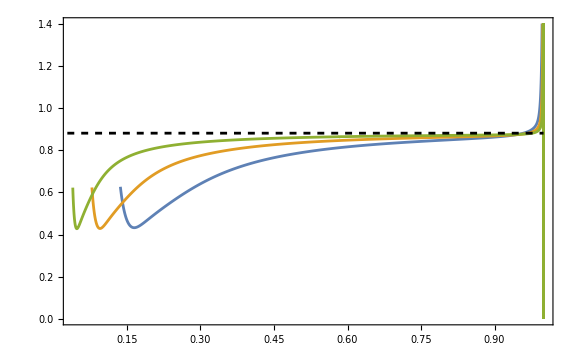

```mathematica
xPlot=Block[{t1=t1grid[[-1]],t2=t1grid[[-1]]/10,t3=t1grid[[-1]]/100,x=(Sqrt[fλ''[1]]/fλ'[1]-1/Sqrt[fλ''[1]])},QKinter[θ_]=Interpolation[Transpose[{θpoints,QK[[bsearch[t1grid,t1]]]}]][θ];
QKinter2[θ_]=Interpolation[Transpose[{θpoints,QK[[bsearch[t1grid,t2]]]}]][θ];
QKinter3[θ_]=Interpolation[Transpose[{θpoints,QK[[bsearch[t1grid,t3]]]}]][θ];
QRinter[θ_]=Interpolation[Transpose[{θpoints,QR[[bsearch[t1grid,t1]]]}]][θ];QRinter2[θ_]=Interpolation[Transpose[{θpoints,QR[[bsearch[t1grid,t2]]]}]][θ];
QRinter3[θ_]=Interpolation[Transpose[{θpoints,QR[[bsearch[t1grid,t3]]]}]][θ];
Show[ListPlot[Transpose[Table[{{QKinter3[θ],(t3 QRinter3[θ])/QKinter3'[θ]},{QKinter2[θ],(t2 QRinter2[θ])/QKinter2'[θ]},{QKinter[θ],(t1 QRinter[θ])/QKinter'[θ]}},{θ,θpoints}]],PlotRange->{{QK[[-1,1]],1},{0.00001,If[γ==0,1.4,1.1/γ]}},Joined->True,Axes->False,AxesStyle->Directive[Black,FontSize->15,FontFamily->"Times"],Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameTicksStyle->{{Directive[FontFamily->"Times New Roman",FontSize->20,Black],Directive[FontOpacity->0,FontSize->0]},{Directive[FontFamily->"Times New Roman",FontSize->20,Black],Directive[FontOpacity->0,FontSize->0]}},ImageSize->Large,FrameStyle->Directive[Black,Thickness[.003]],FrameLabel->{MaTeX["C(t_1,t_2)",Magnification->2.5],MaTeX["x(C)",Magnification->2.5]},PlotLegends->Placed[MaTeX["t_1="<>ToString[Round[#]],Magnification->1.4]&/@{t3,t2,t1},If[γ==0,{0.85,0.25},{0.2,0.75}]]],Plot[x,{θ,0,1},PlotStyle->Directive[Black,Dashed]]]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","x39.pdf"}],xPlot];
```

```mathematica
Clear[hfunc,Q];
hfunc[t_,t2_,α_:1]:=Block[{tpos=bsearch[t1grid,t],dataH},QKinter[θ_]=Interpolation[Transpose[{θpoints,QK[[tpos]]}],Method->"Spline",InterpolationOrder->3][θ];
dQKinter[θ_]=Interpolation[Transpose[{θpoints,(QK[[tpos+1]]-QK[[tpos]])/(t1grid[[tpos+1]]-t1grid[[tpos]])}],Method->"Spline",InterpolationOrder->3][θ];

dataH=Exp[-α Reverse[Prepend[Accumulate[Reverse[Table[-(QKinter'[θ]/t)/(dQKinter[θ]-θ/t QKinter'[θ]),{θ,θpoints}]].secInt5],0]]];
Interpolation[Transpose[{t θpoints,dataH}],Method->"Spline",InterpolationOrder->3][t2]];
Q[t_,x_]:=Interpolation[Transpose[{hfunc[t,t θpoints],QKinter[θpoints]}],Method->"Spline",InterpolationOrder->3][x];

QLog[t_,x_]:=Interpolation[DeleteDuplicatesBy[Join[Transpose[{Subdivide[Log[QK[[-1,1]]]-0.001,Log[QK[[bsearch[t1grid,t],1]]],10],ConstantArray[-1,11]}],Transpose[{Log[QK[[bsearch[t1grid,t],1]]]-Log[QK[[bsearch[t1grid,t θpoints],1]]],QK[[bsearch[t1grid,t]]]}]],First],Method->"Spline",InterpolationOrder->1][x];
```

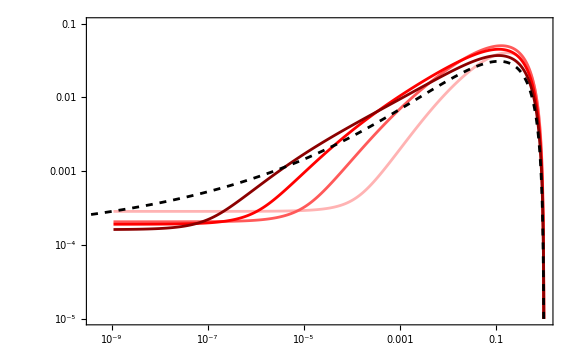

```mathematica
plot=Block[{tmax=t1grid[[-2]],μ=0.89},Show[ListLogLogPlot[Evaluate@Table[Transpose[{θpoints,hfunc[t,t θpoints]-θpoints}],{t,10^Range[-3,0] tmax}],PlotRange->{10^-5,.1},FrameLabel->{MaTeX["t_2/t_1",Magnification->2.5],MaTeX["h(t_2)-t_2/t_1",Magnification->2.5]},PlotLabel->MaTeX["p=3,\\;\\; s=9,\\;\\; \\lambda=0.5",Magnification->1.8],Joined->True,PlotStyle->Join[Lighter[Red,#]&/@Most[Subdivide[0.7,0.,2]],Darker[Red,#]&/@Most[Subdivide[0,0.9,2]]],Evaluate[style],Epilog->{Inset[Show[ListPlot[Evaluate@Table[Transpose[{θpoints,hfunc[t,t θpoints]-θpoints}],{t,10^Range[-3,0] tmax}],Joined->True,PlotStyle->Join[Lighter[Red,#]&/@Most[Subdivide[0.7,0.,2]],Darker[Red,#]&/@Most[Subdivide[0,0.9,2]]],Evaluate[styleInset]],Plot[Exp[1/(1-μ)(x^(1-μ)-1)]-x,{x,0,1},PlotStyle->Directive[Black,Dashed]]],{Log[5*10^-8],Log[9*10^-3]},Automatic,Scaled[.43]]}],LogLogPlot[Exp[1/(1-μ)(x^(1-μ)-1)]-x,{x,10^-10,1},PlotStyle->Directive[Black,Dashed]]]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","h39.pdf"}],plot];
```

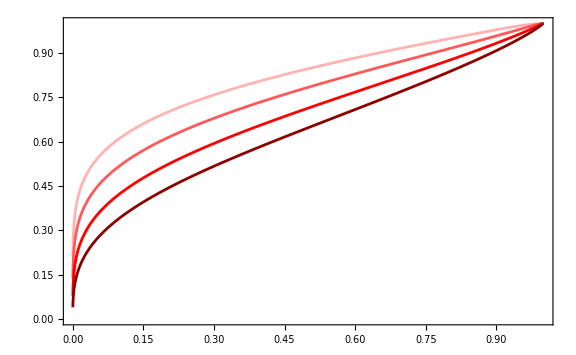

```mathematica
Block[{tmax=t1grid[[-2]]},ListPlot[Table[Block[{θmod=hfunc[t,t θpoints[[1]]]+(1-hfunc[t,t θpoints[[1]]])θpoints},Transpose[{θmod,Q[t,θmod]}]],{t,10^Range[-3,0] tmax}],FrameLabel->{MaTeX["x",Magnification->2.5],MaTeX["\\mathcal{C}(x)",Magnification->2.5]},PlotLabel->MaTeX["p=3,\\;\\; s=9,\\;\\; \\lambda=0.5",Magnification->1.8],PlotStyle->Join[Lighter[Red,#]&/@Most[Subdivide[0.7,0.,2]],Darker[Red,#]&/@Most[Subdivide[0,0.9,2]]],Joined->True,Evaluate[style],Epilog->{Inset[Show[ListLogLogPlot[Table[Block[{θmod=hfunc[t,t θpoints[[1]]]+(1-hfunc[t,t θpoints[[1]]])θpoints},Transpose[{θmod,Q[t,θmod]}]],{t,10^Range[-3,0] tmax}],Joined->True,PlotStyle->Join[Lighter[Red,#]&/@Most[Subdivide[0.7,0.,2]],Darker[Red,#]&/@Most[Subdivide[0,0.9,2]]],Evaluate[styleInset]]],{0.71,.31},Automatic,Scaled[.56]]}]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","c39.pdf"}],plot];
```

```mathematica
QK=data[["Data","QKv"]];
QR=data[["Data","QRv"]];
```

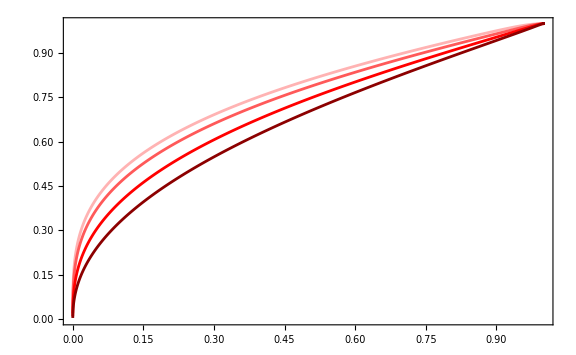

```mathematica
plot=Block[{tmax=t1grid[[-2]]},ListPlot[Table[Block[{θmod=hfunc[t,t θpoints34[[1]]]+(1-hfunc[t,t θpoints34[[1]]])θpoints34},Transpose[{θmod,Q[t,θmod]}]],{t,10^Range[-3,0] tmax}],FrameLabel->{MaTeX["x",Magnification->2.5],MaTeX["\\mathcal{C}(x)",Magnification->2.5]},PlotLabel->MaTeX["p=3,\\;\\; s=4,\\;\\; \\lambda=0.5",Magnification->1.8],PlotStyle->Join[Lighter[Red,#]&/@Most[Subdivide[0.7,0.,2]],Darker[Red,#]&/@Most[Subdivide[0,0.9,2]]],Joined->True,Evaluate[style],Epilog->{Inset[Show[ListLogLogPlot[Table[Block[{θmod=hfunc[t,t θpoints34[[1]]]+(1-hfunc[t,t θpoints34[[1]]])θpoints34},Transpose[{θmod,Q[t,θmod]}]],{t,10^Range[-3,0] tmax}],Joined->True,PlotStyle->Join[Lighter[Red,#]&/@Most[Subdivide[0.7,0.,2]],Darker[Red,#]&/@Most[Subdivide[0,0.9,2]]],Evaluate[styleInset]]],{0.71,.31},Automatic,Scaled[.56]]}]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","c34.pdf"}],plot];
```

```mathematica
dir="/nobackups/jlang/Results_CPC/04_12_2025_0128_p=3_q=3_lambda=0.50_T0=inf_G=0.00_L=512";
t1grid=Rest[Import[FileNameJoin[{dir,"rvec.txt"}],"Table"]][[All,1]];
θpoints=Developer`ToPackedArray[1.Flatten[Import[FileNameJoin[{dir,"t1_compressed.txt"}],"Table"]]];
θpoints*=1/θpoints[[-1]];
QK=LoadCompressed[FileNameJoin[{dir,"QK_compressed"}]];

Clear[QKfunc];
QKfunc[t1_,θ_]=Interpolation[Transpose[{Flatten[ConstantArray[θpoints*t1grid[[-1]],Length[θpoints]]],Flatten[Transpose[ConstantArray[θpoints,Length[θpoints]]]],Flatten[Transpose[QK]]}],Method->"Spline",InterpolationOrder->3][t1,θ];
```

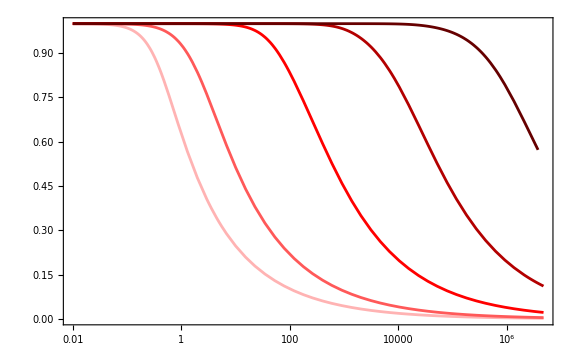

```mathematica
plot=LogLinearPlot[Evaluate[Table[QKfunc[tw+τ,tw/(tw+τ)]+ⅈ HeavisideTheta[tw+τ-t1grid[[-1]]],{tw,Prepend[100^Range[0,3],0]}]],{τ,0.01,t1grid[[-1]]},PlotStyle->Join[Lighter[Red,#]&/@Most[Subdivide[0.7,0.,2]],Darker[Red,#]&/@Most[Subdivide[0,0.9,3]]],Evaluate[style],FrameLabel->{MaTeX["t",Magnification->2.5],MaTeX["C(t_w+\\tau,t_w)",Magnification->2.5]},PlotLegends->Placed[Prepend[Table[MaTeX["t_w="<>ToString[100^n],Magnification->1.6],{n,0,33}],MaTeX["t_w=0",Magnification->1.6]],{0.2,0.3}]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","Cwaiting.pdf"}],plot];
```

```mathematica
dir="/nobackups/jlang/Results_CPC/03_12_2025_1938_p=3_q=9_lambda=0.50_T0=inf_G=0.00_L=2048/";
t1grid=Rest[Import[FileNameJoin[{dir,"rvec.txt"}],"Table"]][[All,1]];
θpoints=Developer`ToPackedArray[1.Flatten[Import[FileNameJoin[{dir,"t1_compressed.txt"}],"Table"]]];
θpoints*=1/θpoints[[-1]];
QK=LoadCompressed[FileNameJoin[{dir,"QK_compressed"}]];

Clear[QKfunc];
QKfunc[t1_,θ_]=Interpolation[Transpose[{Flatten[ConstantArray[θpoints*t1grid[[-1]],Length[θpoints]]],Flatten[Transpose[ConstantArray[θpoints,Length[θpoints]]]],Flatten[Transpose[QK]]}],Method->"Spline",InterpolationOrder->3][t1,θ];
```

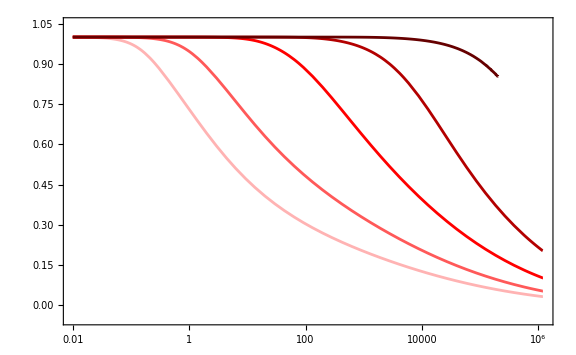

```mathematica
plot=LogLinearPlot[Evaluate[Table[QKfunc[tw+τ,tw/(tw+τ)]+ⅈ HeavisideTheta[tw+τ-t1grid[[-1]]+30000],{tw,Prepend[100^Range[0,3],0]}]],{τ,0.01,t1grid[[-1]]},PlotRange->{-0.05,1.05},PlotStyle->Join[Lighter[Red,#]&/@Most[Subdivide[0.7,0.,2]],Darker[Red,#]&/@Most[Subdivide[0,0.9,3]]],Evaluate[style],FrameLabel->{MaTeX["t",Magnification->2.5],MaTeX["C(t_w+\\tau,t_w)",Magnification->2.5]},PlotLegends->Placed[Prepend[Table[MaTeX["t_w="<>ToString[100^n],Magnification->1.6],{n,0,3}],MaTeX["t_w=0",Magnification->1.6]],{0.2,0.33}]]
Export[FileNameJoin[{ParentDirectory[NotebookDirectory[],2],"Plots","CwaitingMixed.pdf"}],plot];
```